## 1st Nov 2018 on crest

```mathematica
datraw20181101 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\01\\qscan20181101-160720.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181101[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is VC laser brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 2nd Nov 2018 on crest

```mathematica
datraw20181102 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\02\\QE scan\\qscan20181102-092138.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181102[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is VC laser brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffpwer =datraw20181102[[All,11]]-datraw20181101[[All,11]];
```

```mathematica
diffpwrdat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffpwer}];
```

```mathematica
plot = ListPointPlot3D[diffpwrdat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is difference \n in laser power from 1st to 2nd Nov '18",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

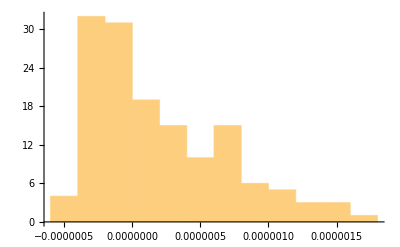

```mathematica
Histogram [diffpwer]
```

```mathematica
Mean[diffpwer]
```

1.97354×10^-7

## 9th November 2018 on crest

```mathematica
datraw20181109a = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan20181109-085332.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
datraw20181109b = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan0915merged.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 13th November on crest

```mathematica
datraw20181113 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\13\\qscan20181113-162002.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181113[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20181109a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is laser power in uJ",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
datraw20181109b = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2018\\11\\09\\qscan0915merged.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20181109b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## !!2019!! 14th Jan (gun phase = ?)

```mathematica
datraw20190114 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\01\\14\\qscan20190114-125000.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190114[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 17 th Jan 2019 on crest

```mathematica
datraw20190117 = Import["W:\\qscan\\qscan20190117-190731.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190117[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20181109b[[All,9]]-datraw20181102[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20181101[[All,5]],datraw20181101[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge differnce \n 2nd to 9th Nov '18 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 28 th Jan 2019 on crest

```mathematica
datraw20190128 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\01\\28\\qscan20190128-185812.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190128[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190128[[All,9]]-datraw20190117[[All,9]]);
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
diffchargedat = Transpose[{datraw20190128[[All,5]],datraw20190117[[All,7]],diffcharge}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 17th to 28th Jan in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.},Symbol[],{46.5928-Symbol[],75.3662-Symbol[],75.2485-Symbol[],63.7706-Symbol[],75.4315-Symbol[],97.237-Symbol[],101.682-Symbol[],108.833-Symbol[],104.832-Symbol[],99.7078-Symbol[],92.8446-Symbol[],66.2544-Symbol[],98.1914-Symbol[],126.389-Symbol[],141.096-Symbol[],133.527-Symbol[],121.134-Symbol[],103.002-Symbol[],97.7992-Symbol[],84.1773-Symbol[],85.6937-Symbol[],88.7658-Symbol[],86.2428-Symbol[],77.9023-Symbol[],83.6021-Symbol[],96.6357-Symbol[],87.4586-Symbol[],93.4067-Symbol[],95.0277-Symbol[],110.349-Symbol[],118.493-Symbol[],126.167-Symbol[],135.109-Symbol[],145.672-Symbol[],144.339-Symbol[],84.2557-Symbol[],109.865-Symbol[],126.507-Symbol[],137.331-Symbol[],130.089-Symbol[],124.677-Symbol[],101.63-Symbol[],92.4262-Symbol[],90.6222-Symbol[],90.8183-Symbol[],92.6223-Symbol[],86.3212-Symbol[],80.0985-Symbol[],75.693-Symbol[],81.1444-Symbol[],88.5044-Symbol[],92.6616-Symbol[],95.0931-Symbol[],98.4005-Symbol[],123.487-Symbol[],131.383-Symbol[],132.847-Symbol[],141.293-Symbol[],133.867-Symbol[],103.146-Symbol[],115.134-Symbol[],136.495-Symbol[],142.09-Symbol[],140.077-Symbol[],125.684-Symbol[],130.795-Symbol[],110.271-Symbol[],105.068-Symbol[],98.6358-Symbol[],83.6413-Symbol[],70.4246-Symbol[],58.816-Symbol[],68.0454-Symbol[],71.9019-Symbol[],94.4787-Symbol[],111.526-Symbol[],115.97-Symbol[],128.403-Symbol[],148.038-Symbol[],139.266-Symbol[],144.155-Symbol[],139.397-Symbol[],104.244-Symbol[],88.6613-Symbol[],73.8105-Symbol[],117.225-Symbol[],121.134-Symbol[],146.744-Symbol[],147.149-Symbol[],170.759-Symbol[],128.468-Symbol[],115.225-Symbol[],107.486-Symbol[],82.9615-Symbol[],77.5232-Symbol[],65.3262-Symbol[],73.6275-Symbol[],81.968-Symbol[],98.3875-Symbol[],108.767-Symbol[],118.402-Symbol[],144.012-Symbol[],162.81-Symbol[],142.064-Symbol[],103.983-Symbol[],91.0928-Symbol[],72.647-Symbol[],22.6303-Symbol[],24.6043-Symbol[],51.4037-Symbol[],62.6724-Symbol[],89.3018-Symbol[],107.983-Symbol[],119.84-Symbol[],126.311-Symbol[],120.088-Symbol[],114.088-Symbol[],80.5169-Symbol[],84.0858-Symbol[],74.9086-Symbol[],58.7506-Symbol[],89.9816-Symbol[],93.7989-Symbol[],99.1718-Symbol[],103.577-Symbol[],114.624-Symbol[],90.8052-Symbol[],59.8487-Symbol[],63.5483-Symbol[],31.546-Symbol[],19.9373-Symbol[],11.6753-Symbol[],4.10611-Symbol[],5.24344-Symbol[],10.7863-Symbol[],26.2123-Symbol[],44.0044-Symbol[],65.2347-Symbol[],76.8696-Symbol[],82.0595-Symbol[],76.229-Symbol[],64.8033-Symbol[],54.4104-Symbol[],57.8224-Symbol[]}}],ColorFunction→Rainbow,PlotLabel→Colour is charge difference 
 17th to 28th Jan in pC,AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## 4 th March 2019 on crest

```mathematica
datraw20190304 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\04\\qscan20190304-111110.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190304[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190304[[All,9]]-datraw20190128[[All,9]]);
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
diffchargedat = Transpose[{datraw20190304[[All,5]],datraw20190128[[All,7]],diffcharge}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 28thJan19 to 04thMar19 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,«19»,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,«94»},«6»[],{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{«1»}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.36364,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,3.72727,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.09091,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.45455,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,4.81818,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.18182,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.54545,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,5.90909,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.27273,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,6.63636,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.,7.},Symbol[],{0.878512-Symbol[],1.04373-Symbol[],2.82442-Symbol[],6.41896-Symbol[],9.41799-Symbol[],13.3577-Symbol[],14.1898-Symbol[],13.4137-Symbol[],14.4445-Symbol[],8.80348-Symbol[],6.6303-Symbol[],1.25476-Symbol[],13.6178-Symbol[],19.1618-Symbol[],26.6757-Symbol[],27.5432-Symbol[],27.9904-Symbol[],28.6994-Symbol[],25.2552-Symbol[],24.1891-Symbol[],17.3678-Symbol[],16.6004-Symbol[],13.7053-Symbol[],1.70901-Symbol[],24.0003-Symbol[],37.5468-Symbol[],40.8392-Symbol[],44.2955-Symbol[],44.947-Symbol[],48.5342-Symbol[],54.5795-Symbol[],53.5779-Symbol[],51.7038-Symbol[],48.3092-Symbol[],43.0078-Symbol[],26.639-Symbol[],57.3192-Symbol[],56.7864-Symbol[],71.5592-Symbol[],71.8916-Symbol[],68.0382-Symbol[],58.5866-Symbol[],53.1902-Symbol[],54.9907-Symbol[],56.4468-Symbol[],54.2768-Symbol[],48.418-Symbol[],32.2173-Symbol[],36.3644-Symbol[],48.5869-Symbol[],58.7312-Symbol[],60.7235-Symbol[],51.9422-Symbol[],59.372-Symbol[],61.3795-Symbol[],77.0754-Symbol[],72.689-Symbol[],79.6338-Symbol[],67.1595-Symbol[],45.07-Symbol[],75.0936-Symbol[],85.892-Symbol[],85.361-Symbol[],76.8182-Symbol[],68.6883-Symbol[],61.5483-Symbol[],52.0497-Symbol[],50.7088-Symbol[],64.2058-Symbol[],62.3632-Symbol[],53.8439-Symbol[],32.3851-Symbol[],41.5303-Symbol[],54.193-Symbol[],60.558-Symbol[],53.2991-Symbol[],49.9752-Symbol[],49.5745-Symbol[],53.4906-Symbol[],62.9043-Symbol[],79.3121-Symbol[],82.0703-Symbol[],86.8116-Symbol[],55.956-Symbol[],65.6936-Symbol[],89.2628-Symbol[],86.7754-Symbol[],68.0926-Symbol[],56.4718-Symbol[],53.0684-Symbol[],44.2777-Symbol[],49.5465-Symbol[],54.7574-Symbol[],53.5271-Symbol[],49.6792-Symbol[],41.0254-Symbol[],38.8724-Symbol[],51.1615-Symbol[],49.8596-Symbol[],48.0344-Symbol[],46.4135-Symbol[],53.7836-Symbol[],59.561-Symbol[],75.3589-Symbol[],89.0373-Symbol[],92.0752-Symbol[],81.9521-Symbol[],56.9418-Symbol[],45.5917-Symbol[],79.5519-Symbol[],98.0168-Symbol[],95.2517-Symbol[],78.824-Symbol[],70.7246-Symbol[],57.3507-Symbol[],56.1891-Symbol[],57.1053-Symbol[],55.9338-Symbol[],44.8029-Symbol[],38.8296-Symbol[],33.7447-Symbol[],54.6093-Symbol[],74.0803-Symbol[],75.0617-Symbol[],70.781-Symbol[],74.0397-Symbol[],86.4112-Symbol[],91.9737-Symbol[],74.1609-Symbol[],53.2652-Symbol[],48.2597-Symbol[],34.698-Symbol[],14.613-Symbol[],32.0536-Symbol[],43.8524-Symbol[],57.2174-Symbol[],71.0899-Symbol[],98.2906-Symbol[],81.4465-Symbol[],78.5104-Symbol[],75.428-Symbol[],70.8497-Symbol[],56.5637-Symbol[],34.0073-Symbol[]}}],ColorFunction→Rainbow,PlotLabel→Colour is charge difference 
 28thJan19 to 04thMar19 in pC,AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## 8 th March 2019 on crest

```mathematica
datraw20190308 = Import["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\08\\qscan20190308-124749.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190308[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
diffcharge =(datraw20190308[[All,9]]-datraw20190304[[All,9]]);
```

```mathematica
diffchargedat = Transpose[{datraw20190308[[All,5]],datraw20190304[[All,7]],diffcharge}];
```

```mathematica
plot = ListPointPlot3D[diffchargedat, ColorFunction->"Rainbow",PlotLabel->Style["Colour is charge difference \n 04thMar19 to 08thMar19 in pC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 14 th March 2019 laser work 1st scan INSTANTEOUS VALUES

```mathematica
datraw20190314a = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190314-113515.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190314a[[All,{5,7,11}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser power Joules",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190314a[[All,{5,7,13}]], ColorFunction->"Rainbow",PlotLabel->Style["VC Brightness PixelCount",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

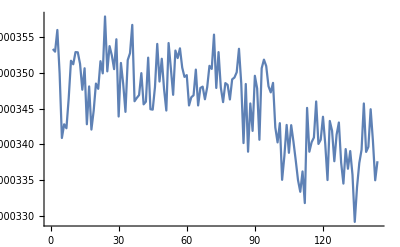

```mathematica
ListPlot[Flatten@datraw20190314a[[All,{11}]],Joined->True]
```

## 14 th March 2019 laser work 2nd scan

```mathematica
datraw20190414b = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190314-140352.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190414b[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser power J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190414b[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC Brightness PixelCount",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

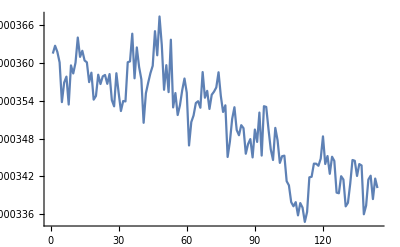

```mathematica
ListPlot[Flatten@datraw20190414b[[All,{14}]],Joined->True]
```

## 15 th March 2019 scan without aperture

```mathematica
datraw20190315a = Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190315-101757.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Charge PC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser Energy J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315a[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315a[[All,9]]/datraw20190315a[[All,14]];
ratioQbyE = Transpose[{datraw20190315a[[All,5]],datraw20190315a[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 15 th March 2019 scan with aperture

```mathematica
datraw20190315b= Import["\\\\apclara1\\ControlRoomApps\\Stage\\Software\\Apps\\qscan\\qscan20190315-132512.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,9}]], ColorFunction->"Rainbow",PlotLabel->Style["Charge PC",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Laser Energy J",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190315b[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## 15 th March VC images Aperture In/Out

I don' t quite understand/remember the sequence of these plots in time. Seems I’ve got aperture in, then aperture out images. The aperture was probably taken out at end of shift as there was a shift on 16th march with beam.

```mathematica
vcimagefiles = FileNames["\\\\claraserv3\\CameraImages\\2019\\3\\15\\*"]
```

{\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_13-24-50_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-2-11_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-2-53_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-5-7_1images.hdf5,\\claraserv3\CameraImages\2019\3\15\VIRTUAL_CATHODE_2019-3-15_14-6-0_1images.hdf5}

```mathematica
alldat = Import[#,"Data"]  &/@  vcimagefiles;
MatrixPlot[#[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,500}]]&),ColorFunctionScaling->False,ImageSize->500] &/@ alldat
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[alldat[[3]][[1]][[800;;1400,900;;1700]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{50,2000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
MatrixPlot[alldat[[5]][[1]][[900;;1500,700;;1500]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{50,2000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

## 27 th March 2019 CATHODE REMOVED, APERTURE IN 1st scan at 1220

```mathematica
datraw20190327a= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190327-122133.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,26}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1} cannot be transposed.

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1.} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],1.}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],1.}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{Symbol[],Symbol[],1}],ColorFunction→Rainbow,PlotLabel→Charge/laser_energy (pC/J),AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## VC images for the above scan

```mathematica
list = FileNames["\\\\claraserv3\\CameraImages\\2019\\3\\27\\VIRTUAL*.hdf5"][[4;;148]];
```

```mathematica
datlist = Import[#,"Data"] & /@ list;
```

```mathematica
Dimensions[datlist]
```

```mathematica
datalistT = Total[datlist]
```

<|/Capture000001→{1}|>
 |  |  |  |

```mathematica
MatrixPlot[datalistT[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{2000,25000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

## 27 th March 2019 CATHODE REMOVED, APERTURE IN 2nd scan

```mathematica
datraw20190327b= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190327-152019.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190327b[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327b[[All,{5,7,26}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03],ImageSize->500,PlotRange->All]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327b[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## test images from new camera

```mathematica
dat = Import["\\\\claraserv3\\CameraImages\\2019\\3\\27\\S01-CAM-01_2019-3-27_17-1-19_1images.hdf5","Data"];  
MatrixPlot[dat[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,4000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
dat = Import["\\\\claraserv3\\CameraImages\\2019\\3\\27\\S01-CAM-01_2019-3-27_17-33-5_1images.hdf5","Data"];  
MatrixPlot[dat[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,400}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

## 27 th March 2019 CATHODE REMOVED, APERTURE IN 3rd scan, photodiode at CATHODE replaced by CAMERA

```mathematica
datraw20190327c= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190327-173039.txt","Table"];
```

```mathematica
plot = ListPointPlot3D[datraw20190327c[[All,{5,7,14}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327c[[All,{5,7,26}]], ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03],ImageSize->500,PlotRange->All]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327c[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

## VC and Screen images for the above scan

```mathematica
list = FileNames["\\\\claraserv3\\CameraImages\\2019\\3\\27\\VIRTUAL*.hdf5"][[-36;;-1]];
```

```mathematica
datlist = Import[#,"Data"] & /@ list;
```

```mathematica
Dimensions[datlist]
```

{36}

```mathematica
datalistT = Total[datlist]
```

<|/Capture000001→{1}|>
 |  |  |  |

```mathematica
MatrixPlot[datalistT[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{2000,5000}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
dlist = FileNames["\\\\claraserv3\\CameraImages\\2019\\3\\27\\S01*.hdf5"][[-36;;-1]]
```

{\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-31-28_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-32-1_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-32-24_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-32-45_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-33-26_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-33-5_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-34-31_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-34-55_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-34-6_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-35-22_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-35-49_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-36-11_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-36-34_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-36-57_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-37-26_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-37-51_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-38-11_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-38-33_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-39-30_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-39-5_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-39-55_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-40-19_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-40-40_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-41-20_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-41-41_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-42-14_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-42-38_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-43-2_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-43-27_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-43-51_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-44-19_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-44-48_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-45-18_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-45-44_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-46-31_1images.hdf5,\\claraserv3\CameraImages\2019\3\27\S01-CAM-01_2019-3-27_17-46-7_1images.hdf5}

```mathematica
datdlist = Import[#,"Data"] & /@ dlist;
```

```mathematica
Dimensions@datdlist[[1]][[1]]
```

{2560,2160}

```mathematica
datdlistC =  (Reverse@(Reverse/@(Transpose@datdlist[[1]][[1]])))
```

{1}
 |  |  |  |

```mathematica
datdlistC =  (Reverse@(Reverse/@(Transpose@#[[1]]))) &/@  datdlist[[1;;36]];
```

```mathematica
datadlistT = Total[datdlist]
```

<|/Capture000001→{1}|>
 |  |  |  |

```mathematica
datadlistTC = Total[datdlistC];
```

```mathematica
MatrixPlot[datadlistTC,ColorFunction->(ColorData["Rainbow"][Rescale[#,{3000,4500}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

-Graphics-

```mathematica
MatrixPlot[datadlistT[[1]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{3500,4500}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

```mathematica
MatrixPlot[datdlist[[25,1]][[1200;;1700,700;;1500]],ColorFunction->(ColorData["Rainbow"][Rescale[#,{100,300}]]&),ColorFunctionScaling->False,ImageSize->500]
```

-Graphics-

## 28th March 2019 CATHODE REMOVED, APERTURE IN 1st scan at 1326

```mathematica
datraw20190328a= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190328-132638.txt","Table"];
```

```mathematica
pd1c1 = 1.31*10^-7
pd1c0 = -7.512
```

1.31×10^-7

-7.512

```mathematica
testdat = Transpose[{datraw20190328a[[All,5]],datraw20190328a[[All,7]],pd1c1 *datraw20190328a[[All,14]]+pd1c0 }];
```

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03],ImageSize->400]
```

-Graphics3D-

```mathematica
ListPlot3D[testdat]
```

-Graphics3D-

```mathematica
pd2c1 = 3.493*10^-6
pd2c0 = -200.5
```

3.493×10^-6

-200.5

```mathematica
testdat = Transpose[{datraw20190328a[[All,5]],datraw20190328a[[All,7]],pd2c1*datraw20190328a[[All,26]]+pd2c0}];
```

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03], PlotRange->All,ImageSize->700]
```

-Graphics3D-

```mathematica
pd1new  = 18.3*(pd1c1 *datraw20190328a[[All,14]]+pd1c0 );

pd2new = 1.34*(pd2c1*datraw20190328a[[All,26]]+pd2c0);
```

```mathematica
ratio = pd2new/pd1new
```

{0.0192207,0.438871,0.565899,0.569664,0.6185,0.601791,0.632925,0.625624,0.599186,0.604839,0.573443,0.567279,0.692671,0.656318,0.585024,0.604938,0.648382,0.680423,0.688797,0.662957,0.718289,0.713948,0.4794,0.0619685,0.166505,0.68024,0.716391,0.711363,0.67338,0.737818,0.716667,0.646841,0.577191,0.537143,0.598418,0.680618,0.588093,0.539713,0.592163,0.657707,0.757798,0.759589,0.725218,0.654464,0.650051,0.652818,0.604903,0.0169394,0.0301371,0.624135,0.633143,0.600317,0.663619,0.665123,0.724184,0.651265,0.601698,0.531687,0.527034,0.607546,0.577016,0.58992,0.590544,0.622182,0.665246,0.618665,0.61014,0.557994,0.570245,0.605856,0.466969,0.0131802,0.00326745,0.624687,0.626592,0.584562,0.569112,0.614096,0.631481,0.715126,0.742568,0.682591,0.646828,0.630703,0.232411,0.623326,0.73304,0.767249,0.760007,0.716594,0.649348,0.608545,0.608497,0.520906,0.210962,-0.0134144,-0.01873,0.0625585,0.183341,0.277378,0.36129,0.444007,0.488484,0.530318,0.404915,0.271779,0.123251,0.0468323,-0.023342,-0.0195512,0.0227704,0.0650391,0.0853128,0.0847664,0.0603784,0.0215464,0.00521931,-0.021795,-0.0248766,-0.0248877,-0.025625,-0.0251714,-0.0245815,-0.0246459,-0.0233265,-0.0230947,-0.0229454,-0.0239794,-0.0253194,-0.0244868,-0.0250797,-0.0265475,-0.0270746}

```mathematica
testdat = Transpose[{datraw20190328a[[All,5]],datraw20190328a[[All,7]],ratio}];

plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["LBM reflectiveness",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03], PlotRange->All,ImageSize->700]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[datraw20190327a[[All,{5,7,19}]], ColorFunction->"Rainbow",PlotLabel->Style["VC brightness",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

-Graphics3D-

```mathematica
QbyE = datraw20190315b[[All,9]]/datraw20190315b[[All,14]];
ratioQbyE = Transpose[{datraw20190315b[[All,5]],datraw20190315b[[All,7]],QbyE}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1} cannot be transposed.

```mathematica
lot = ListPointPlot3D[ratioQbyE, ColorFunction->"Rainbow",PlotLabel->Style["Charge/laser_energy (pC/J)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03]]
```

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1.} cannot be transposed.

ListPointPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],1.}] must be a valid array or a list of valid arrays.

Transpose::nmtx: The first two levels of {Symbol[],Symbol[],1.} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[{Symbol[],Symbol[],1.}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[Transpose[{Symbol[],Symbol[],1}],ColorFunction→Rainbow,PlotLabel→Charge/laser_energy (pC/J),AxesLabel→{VC x (mm),VC y (mm)},AxesStyle→15,ViewPoint→{0,0,∞},PlotLegends→True,PlotStyle→PointSize[0.03]]

## 28th March 2019 CATHODE REMOVED, APERTURE IN 2st scan at 1545

```mathematica
datraw20190328b= Import["C:\\Users\\fj38.CLRC\\Documents\\GitHub\\Software\\Apps\\qscan\\qscan20190328-154530.txt","Table"];
```

```mathematica
pd1c1 = 1.31*10^-7
pd1c0 = -7.512
```

1.31×10^-7

-7.512

```mathematica
testdat = Transpose[{datraw20190328b[[All,5]],datraw20190328b[[All,7]],pd1c1 *datraw20190328b[[All,14]]+pd1c0 }];
```

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 1 in laser transport (uJ)",20],AxesLabel->{Style["VC x (mm)",20],Style["VC y (mm)",20]},AxesStyle->15,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03],ImageSize->600,PlotRange->All]
```

-Graphics3D-

```mathematica
pd2c1 = 3.493*10^-6
pd2c0 = -200.5
```

3.493×10^-6

-200.5

```mathematica
testdat = Transpose[{datraw20190328b[[All,5]],datraw20190328b[[All,7]],pd2c1*datraw20190328b[[All,26]]+pd2c0}];
```

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03], PlotRange->All,ImageSize->600]
```

-Graphics3D-

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03], PlotRange->All,ImageSize->600]
```

-Graphics3D-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
plot = ListPointPlot3D[testdat, ColorFunction->"GrayTones",PlotLabel->Style["Photodiode 2 at real cathode (A.U.)",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.1], PlotRange->All,ImageSize->600]
```

-Graphics3D-

```mathematica
ListPlot3D[testdat]
```

-Graphics3D-

```mathematica
pd1c1 *datraw20190328b[[All,14]]+pd1c0
```

{1.13449,1.17015,1.11579,1.15319,1.14412,1.15038,1.14436,1.13585,1.14648,1.1508,1.13271,1.15822,1.11752,1.09307,1.04478,0.993656,0.8941,0.931987,1.01055,1.08513,1.10797,1.11108,1.10263,1.14274,1.12331,1.13185,1.14263,1.14512,1.14006,1.15046,1.14946,1.13218,1.12038,1.13032,1.11494,1.1373,1.14085,1.14381,1.15293,1.12775,1.11329,1.16216,1.1456,1.13788,1.14036,1.09778,1.08003,1.09306,1.06283,0.986374,0.857722,0.875487,1.00269,1.0649,1.10448,1.09761,1.11697,1.13028,1.10728,1.138,1.09904,1.11388,1.13307,1.13849,1.13449,1.14881,1.16621,1.14693,1.13061,1.15271,1.13847,1.12513,1.15533,1.15279,1.13779,1.13288,1.13226,1.1311,1.14238,1.11641,1.11738,1.04276,1.04362,0.986045,0.872873,0.894824,1.0121,1.0534,1.08226,1.09097,1.112,1.12009,1.09457,1.11714,1.14085,1.14173,1.15178,1.13706,1.13277,1.09188,1.10359,1.1009,1.12578,1.09886,1.09878,1.07275,1.12673,1.123,1.11798,1.1163,1.11032,1.10807,1.09443,1.07939,1.07617,1.05773,1.03405,0.943497,0.840157,0.9123,0.998488,1.01403,1.06663,1.06162,1.09234,1.06581,1.08458,1.07647,1.07193,1.09163,1.07539,1.06474,1.0799,1.07753,1.08979,1.0971,1.12285,1.10691,1.12782,1.13069,1.12503,1.1347,1.11286,1.11991,1.13077,1.13272,1.11316,1.09754,1.06927,1.06522,1.03357,0.96755,0.862432,0.909992,1.00375,1.05914,1.09907,1.0859,1.12295,1.13798,1.12969,1.12813,1.1189,1.14812,1.14294,1.14293,1.14282,1.14801,1.13332,1.12306,1.14295,1.13776,1.13676,1.13505,1.14447,1.12528,1.14076,1.13873,1.14818,1.138,1.14403,1.11757,1.09405,1.08175,1.04798,0.983227,0.915892,0.912892,1.01264,1.09802,1.11272,1.11063,1.11478,1.1217,1.12087,1.10317,1.15025,1.13989,1.163,1.14204,1.15203,1.13724,1.1386,1.13847,1.12526,1.12545,1.11922,1.1429,1.13214,1.12692,1.11061,1.10955,1.09861,1.10245,1.11011,1.09533,1.09517,1.07956,1.02393,0.983915,0.887443,0.916637,1.02366,1.05987,1.09207,1.10002,1.09665,1.13722,1.11673,1.11688,1.12573,1.10361,1.11185,1.13208,1.11583,1.14187,1.14296,1.15062,1.09917,1.10086,1.11952,1.11694,1.10986,1.12752,1.12203,1.11796,1.1224,1.11817,1.11234,1.119,1.09974,1.10592,1.05516,1.01144,0.913864,0.940953,1.04178,1.07739,1.07169,1.09988,1.09549,1.10196,1.10167,1.12798,1.11954,1.10733,1.1151,1.12206,1.08552,1.09059,1.09895,1.10007}

```mathematica
pd2c1*datraw20190328b[[All,26]]+pd2c0
```

{-0.404969,-0.406318,-0.414791,-0.410866,-0.406522,-0.390315,-0.39935,-0.402121,-0.402816,-0.407938,-0.414847,-0.412695,-0.408041,-0.412153,-0.406759,-0.385111,-0.335469,-0.360322,-0.39345,-0.405584,-0.402756,-0.404641,-0.402267,-0.407312,-0.402772,-0.403917,-0.404278,-0.405938,-0.403293,-0.405222,-0.408053,-0.403622,-0.396405,-0.408395,-0.36436,-0.376139,-0.361908,-0.34019,-0.321623,-0.305154,-0.258861,-0.117602,-0.00888241,-0.321174,-0.322002,-0.343481,-0.35263,-0.352534,-0.358644,-0.367914,-0.343025,-0.316217,-0.275431,0.0891378,1.33624,2.01249,2.79359,3.12527,3.2394,3.3642,2.86304,2.48569,2.12105,1.64811,1.19207,0.406512,-0.0843305,-0.351637,0.0103059,5.72459,7.54679,8.11281,8.8456,9.2202,9.22287,9.47134,9.14844,8.62213,8.9708,8.22004,7.90471,6.48262,4.91729,3.133,0.140665,3.15515,9.55375,11.4532,11.2157,10.3846,9.53028,9.0669,9.09793,9.97722,10.3796,10.937,10.5683,10.7625,11.6353,10.9818,8.02604,0.184189,0.967597,9.83962,11.04,10.4475,10.6761,11.1706,11.2611,10.6889,9.36738,8.36118,8.07888,8.82247,10.264,11.2905,12.5233,12.1435,3.04907,6.25186,12.5073,11.0268,9.76437,8.3795,8.10753,8.29168,9.49849,10.6262,11.2463,11.3292,10.5277,9.63364,10.2456,10.2745,6.80159,4.12649,0.700692,9.90041,10.1567,9.43224,9.67736,10.8007,11.253,11.685,10.0397,9.24525,8.31951,8.11455,8.83812,9.60868,11.829,12.4955,3.20038,5.57863,11.99,10.9026,9.26577,8.09963,8.40333,8.884,9.14517,10.1236,10.2096,10.3073,9.44949,9.08578,10.0168,9.96745,5.03062,0.26158,1.25146,8.69777,9.8704,9.86737,9.38544,9.83905,10.2429,10.4844,10.8401,10.1828,10.2221,9.35132,9.26806,10.0139,11.0391,6.81696,1.49386,0.0211811,3.07613,5.96409,8.93575,9.52483,10.5756,11.9347,11.8942,11.2648,10.9832,10.3986,9.71901,9.66501,10.3096,9.81804,5.38697,0.0278854,-0.323839,3.32563,9.53161,9.43834,9.70649,9.9154,10.5796,11.5021,11.7766,10.9339,9.74057,7.11956,3.59962,2.47221,0.6617,-0.332877,-0.370746,-0.393631,-0.372485,-0.338752,0.244746,0.99354,1.88993,3.79795,5.234,6.46219,6.52913,6.03161,4.92569,3.92452,2.56167,1.13575,-0.0204807,-0.361896,-0.373691,-0.378783,-0.314256,-0.309873,-0.193821,0.572016,1.01612,1.05723,0.859548,0.26151,-0.291048,-0.337713,-0.365884,-0.384603,-0.399012,-0.404639,-0.409667,-0.402165,-0.408474,-0.402478,-0.392324,-0.386955,-0.368294,-0.366617,-0.360549,-0.35772,-0.346729,-0.355415,-0.353728,-0.371568,-0.375447,-0.371742,-0.380903,-0.391155}

```mathematica
pd1new  = 18.3*(pd1c1 *datraw20190328b[[All,14]]+pd1c0 );

pd2new = 1.34*(pd2c1*datraw20190328b[[All,26]]+pd2c0);
```

```mathematica
ratio = pd2new/pd1new
```

{-0.0261382,-0.025426,-0.0272209,-0.0260888,-0.0260175,-0.0248443,-0.0255532,-0.0259233,-0.0257273,-0.0259567,-0.0268178,-0.026091,-0.0267364,-0.0276098,-0.028508,-0.0283794,-0.0274739,-0.0283097,-0.0285092,-0.0273686,-0.0266177,-0.0266674,-0.026714,-0.0260996,-0.0262551,-0.026131,-0.0259078,-0.0259575,-0.0259028,-0.0257913,-0.0259942,-0.0261045,-0.0259077,-0.0264565,-0.0239293,-0.0242174,-0.0232287,-0.0217782,-0.0204267,-0.0198134,-0.0170261,-0.00740976,-0.000567741,-0.020668,-0.0206761,-0.0229108,-0.0239075,-0.0236162,-0.0247089,-0.0273123,-0.0292842,-0.0264478,-0.0201141,0.00612923,0.0885891,0.134258,0.183137,0.202468,0.21422,0.216467,0.190751,0.163404,0.137072,0.106001,0.0769407,0.0259107,-0.00529495,-0.0224497,0.000667462,0.363645,0.485394,0.527987,0.560629,0.58566,0.593551,0.612185,0.591637,0.558173,0.575008,0.539141,0.518011,0.455217,0.345015,0.232658,0.0118002,0.258188,0.691198,0.796134,0.758834,0.696996,0.62756,0.592736,0.608628,0.653968,0.666197,0.701432,0.671874,0.693083,0.752121,0.736466,0.532532,0.012251,0.0629352,0.655677,0.735721,0.713129,0.693821,0.728366,0.737561,0.701143,0.617766,0.552529,0.540524,0.598503,0.698377,0.781607,0.886806,0.942446,0.265742,0.501794,0.917222,0.796251,0.670326,0.577964,0.543479,0.569663,0.641281,0.722815,0.768236,0.759935,0.716844,0.662523,0.694718,0.698205,0.457004,0.275417,0.0456942,0.654928,0.659422,0.610837,0.629864,0.696985,0.740426,0.764011,0.65013,0.597654,0.54726,0.541373,0.605238,0.660509,0.838034,0.945657,0.271726,0.448894,0.874679,0.753751,0.617319,0.54617,0.547952,0.571646,0.592768,0.657101,0.668141,0.657374,0.605395,0.5821,0.641813,0.635758,0.325029,0.0170551,0.0801755,0.559772,0.635797,0.63656,0.60049,0.640246,0.657485,0.674182,0.691313,0.65521,0.654268,0.612704,0.620305,0.677849,0.771319,0.507681,0.119432,0.00169896,0.222435,0.397729,0.588031,0.627976,0.694654,0.779092,0.777021,0.747712,0.699183,0.667981,0.611921,0.61969,0.655287,0.63216,0.34644,0.00179354,-0.0210731,0.216372,0.623599,0.604701,0.627793,0.644272,0.697526,0.759075,0.784929,0.726217,0.642498,0.47595,0.240675,0.167684,0.0473199,-0.0247731,-0.0305908,-0.0314446,-0.0266445,-0.0234036,0.0164104,0.0661359,0.126191,0.244546,0.343192,0.423668,0.424694,0.400195,0.324395,0.253842,0.168104,0.072831,-0.00131211,-0.0230305,-0.0248944,-0.0251948,-0.0205545,-0.0203146,-0.0127876,0.0371481,0.0663128,0.0692461,0.0560757,0.0171252,-0.0191594,-0.0220988,-0.0243617,-0.0254651,-0.02769,-0.029294,-0.0328249,-0.0312961,-0.0287107,-0.0273542,-0.0268057,-0.0257614,-0.0246173,-0.0243613,-0.0239643,-0.0232218,-0.022678,-0.0235025,-0.0232279,-0.0242479,-0.0253258,-0.0249593,-0.0253799,-0.0260364}

```mathematica
testdat = Transpose[{datraw20190328b[[All,5]],datraw20190328b[[All,7]],ratio}];

plot = ListPointPlot3D[testdat, ColorFunction->"Rainbow",PlotLabel->Style["LBM reflectiveness",20],AxesLabel->{Style["VC x (mm)",25],Style["VC y (mm)",25]},AxesStyle->25,ViewPoint->{0,0,Infinity},PlotLegends->True,PlotStyle->PointSize[0.03], PlotRange->All,ImageSize->700]
```

-Graphics3D-

```mathematica
plot = ListContourPlot[testdat]
```

-Graphics-

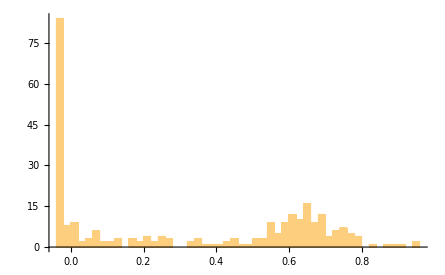

```mathematica
Histogram[testdat[[All,3]],50]
```

```mathematica
ListPlot3D[testdat]
```

-Graphics3D-

## Summary

```mathematica
dates = {1,2,9,13}
```

{1,2,9,13}

```mathematica
maxcharges = Max[#[[All,9]]] &/@ {datraw20181101 ,datraw20181102,datraw20181109,datraw20181113}
```

{183.442,158.189,100.074,90.8967}

```mathematica
maxPlas = Max[#[[All,11]]] &/@ {datraw20181101 ,datraw20181102,datraw20181109,datraw20181113}
```

{9.46534×10^-6,9.26804×10^-6,7.303×10^-6,6.71789×10^-6}

```mathematica
ratio = maxcharges/maxPlas
```

{1.93804×10^7,1.70682×10^7,1.37031×10^7,1.35306×10^7}

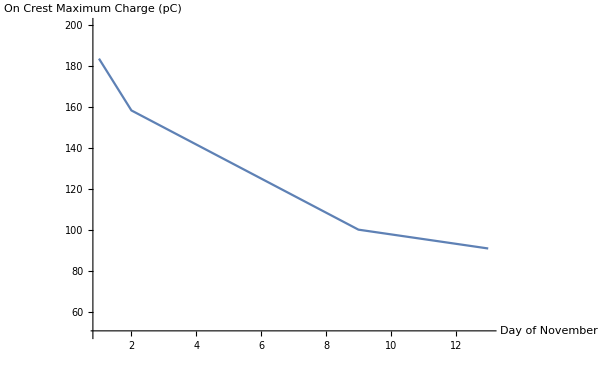

```mathematica
ListPlot[Transpose[{dates,maxcharges}],PlotRange->{All,{50,200}},Joined->True,AxesLabel->{"Day of November","On Crest Maximum Charge (pC)"},AxesStyle->15,ImageSize->600]
```

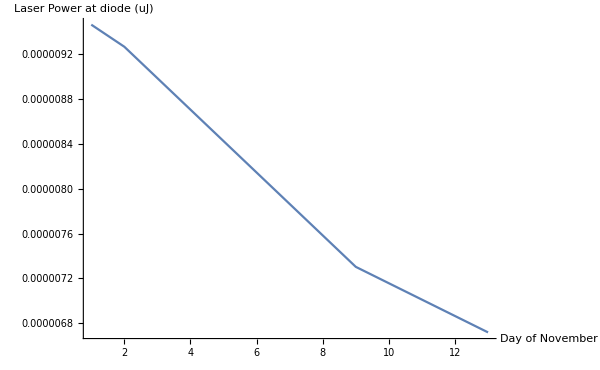

```mathematica
ListPlot[Transpose[{dates,maxPlas}],PlotRange->{All,All},Joined->True,AxesLabel->{"Day of November","Laser Power at diode (uJ)"},AxesStyle->15,ImageSize->600]
```

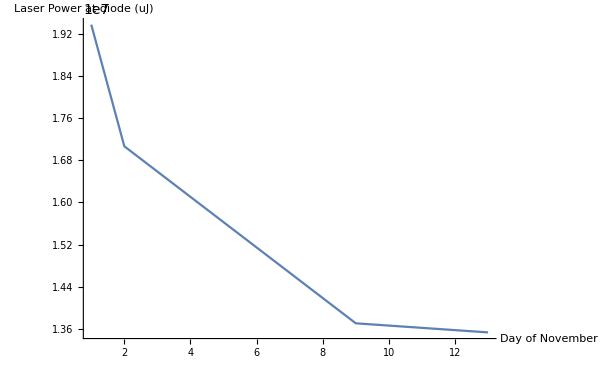

```mathematica
ListPlot[Transpose[{dates,ratio}],PlotRange->{All,All},Joined->True,AxesLabel->{"Day of November","Laser Power at diode (uJ)"},AxesStyle->15,ImageSize->600]
```